```mathematica
ClearAll["Global`*"]
ClearAll[coefF];
SetDirectory[NotebookDirectory[]];
coefF[vars_,basis_,poly_]:=First@@@CoefficientRules[basis,vars]/. CoefficientRules[poly,vars]/. {_,_}:>0

(*Module[{path,nb},path="/Users/panos/Desktop/work in progress/coding/lane_free_dp/mathematica/plotFunctions.nb";
nb=NotebookOpen[path,CellContext->"$Context",Visible->True];
NotebookEvaluate[nb,InsertResults->False];
(*NotebookClose[nb]*)]*)
myPlot[K_,fontSize_]:=Module[{steps,axp,ayp,vxp,vyp,yp},
steps=Table[i,{i,1,K}];
defBlue=ColorData[97,1];defOrange=ColorData[97,2];defGreen=ColorData[97,3];

axp=ListLinePlot[{Transpose[{steps,axInitNext[[1;;K]]}],Transpose[{steps,axInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","ax (m/s/s)",None,None}];
ayp=ListLinePlot[{Transpose[{steps,ayInitNext[[1;;K]]}],Transpose[{steps,ayInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","ay (m/s/s)",None,None}];
vxp=ListLinePlot[{Transpose[{steps,vxInitNext[[1;;K]]}],Transpose[{steps,vxInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","vx (m/s)",None,None}];
vyp=ListLinePlot[{Transpose[{steps,vyInitNext[[1;;K]]}],Transpose[{steps,vyInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","vy (m/s)",None,None}];
yp=ListLinePlot[{Transpose[{steps,yInitNext[[1;;K]]}],Transpose[{steps,yInit[[1;;K]]}]},
Joined->True,PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman", FontSize->fontSize},PlotStyle->{{Thickness[0.007],defOrange},{Thickness[0.007],Dashing[0.01],defBlue}},
FrameLabel->{"Time Steps","y (m)",None,None}];

GraphicsRow[{axp,ayp,vxp,vyp,yp},ImageSize->1700,Spacings->Scaled[0.1],AspectRatio->Full]//Print;
];

simOutput[K_,step_]:=Module[{file},
DeleteFile["sim.js"];
file=CreateFile["sim.js"];

WriteString[file,"sim = {\n"];

(*x*)
WriteString[file,"x: [\n"];
For[idVeh=1,idVeh<=numVeh,idVeh++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", xInitNext[[k]]]];];
WriteString[file,"],\n"];
];
For[idObs=1,idObs<=numObs,idObs++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", xObs[[idObs,k]]]];];
WriteString[file,"],\n"];
];
WriteString[file,"],\n"];
(*y*)
WriteString[file,"y: [\n"];
For[idVeh=1,idVeh<=numVeh,idVeh++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", yInitNext[[k]]]];];
WriteString[file,"],\n"];
];
For[idObs=1,idObs<=numObs,idObs++,
WriteString[file,"["];
For[k=1,k<=K,k++,WriteString[file,StringForm["``,", yObs[[idObs,k]]]];];
WriteString[file,"],\n"];
];
WriteString[file,"],\n"];

(*other parameters*)
WriteString[file,StringForm["k:``,\n",K]];
WriteString[file,StringForm["Step:``,\n",step]];
WriteString[file,StringForm["roadwidth:``,\n",10.0]];
WriteString[file,StringForm["roadlength:``,\n",Max[xInitNext]+50.0]];
WriteString[file,StringForm["n:``,\n",numVeh+numObs]];
WriteString[file,StringForm["Cx:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",5.0]]];
WriteString[file,StringForm["],\n"]];
WriteString[file,StringForm["Cy:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",2.0]]];
WriteString[file,StringForm["],\n"]];
WriteString[file,StringForm["id:["]];
For[i=1,i<=numVeh+numObs,i++,WriteString[file,StringForm["``,",i]]];
WriteString[file,StringForm["],\n"]];

WriteString[file,StringForm["};\n\n"]];

Close[file];
];
```

```mathematica
Read Data;
dx=.;dy=.;dvx=.;dvy=.;dax=.;day=.;
numVeh=1;
K=97;T=0.25;eps=1.0;

vdx=30.0;vdy=0.5;
maxIter=50;epsilon=0.01;
CONSTRAINED=1;
p=5.0;
axMin=-2.0;axMax=1.0;ayMin=-1.0;ayMax=1.0;
w1=1.0;w2=1.0;w3=0.1;w4=0.1;w5=0.0;

yMax=10.0;yMin=0.0;
Klat=1.0;

(*Module[{path,nb},path="/Users/panos/Desktop/work in progress/coding/lane_free_dp/mathematica/data.nb";
nb=NotebookOpen[path,CellContext->"$Context",Visible->True];
NotebookEvaluate[nb,InsertResults->False];
(*NotebookClose[nb]*)]*)

xInit0={15.0000,21.2534,27.5128,33.7763,40.0428,46.3113,52.5811,58.8516,65.1227,71.3938,77.6650,83.9361,90.2068,96.4773,102.7475,109.0172,115.2866,121.5556,127.8241,134.0923,140.3600,146.6274,152.8943,159.1609,165.4271,171.6929,177.9583,184.2234,190.4882,196.7525,203.0166,209.2803,215.5437,221.8068,228.0696,234.3321,240.5943,246.8562,253.1179,259.3792,265.6403,271.9012,278.1617,284.4221,290.6822,296.9420,303.2017,309.4611,315.7202,321.9792,328.2380,334.4965,340.7549,347.0130,353.2710,359.5288,365.7864,372.0438,378.3010,384.5581,390.8150,397.0718,403.3284,409.5848,415.8411,422.0972,428.3532,434.6091,440.8648,447.1204,453.3758,459.6311,465.8863,472.1414,478.3964,484.6512,490.9059,497.1605,503.4150,509.6694,515.9237,522.1779,528.4320,534.6860,540.9399,547.1938,553.4475,559.7011,565.9547,572.2082,578.4615,584.7149,590.9681,597.2212,603.4743,609.7273,615.9803};
vxInit0={25.0000,25.0275,25.0472,25.0611,25.0707,25.0771,25.0811,25.0835,25.0846,25.0849,25.0845,25.0837,25.0826,25.0813,25.0798,25.0783,25.0767,25.0751,25.0734,25.0718,25.0702,25.0686,25.0670,25.0655,25.0640,25.0625,25.0610,25.0596,25.0582,25.0569,25.0556,25.0543,25.0530,25.0518,25.0506,25.0494,25.0482,25.0471,25.0460,25.0449,25.0439,25.0428,25.0418,25.0409,25.0399,25.0390,25.0381,25.0372,25.0363,25.0354,25.0346,25.0338,25.0330,25.0322,25.0315,25.0307,25.0300,25.0293,25.0286,25.0280,25.0273,25.0267,25.0260,25.0254,25.0248,25.0243,25.0237,25.0231,25.0226,25.0221,25.0215,25.0210,25.0205,25.0201,25.0196,25.0191,25.0187,25.0182,25.0178,25.0174,25.0170,25.0166,25.0162,25.0158,25.0154,25.0151,25.0147,25.0144,25.0140,25.0137,25.0134,25.0131,25.0128,25.0125,25.0122,25.0119,25.0116};
axInit0={0.791666666666667,0.758935121279535,0.726213549529528,0.694666367706865,0.664122725850076,0.634402308797146,0.605302204394755,0.576579947650008,0.547929326838863,0.518943345639999,0.489054421051356,0.457433267856378,0.422810001027360,0.383141924893194,0.334962397092913,0.272024101073574,0.182271887858506,0.0405904647549519,-0.209477161924316,-0.697837764870730,-1.62626965264717,-2.36706910442592,-1.47658733784382,-0.540594338689934,-0.0569165419476470,0.190954314697755,0.330833212789906,0.406842738828616,0.438566599355863,0.438915912696000,0.415824392977162,0.373546193195811,0.315589248843642,0.248061876429765,0.179175488153147,0.112452515261920,0.0468058543478525,-0.0124358249439287,-0.0592785787000096,-0.0889519870963955,-0.0965396700192915,-0.0787317186409768,-0.0336085652458849,0.0406281835770721,0.147431771211884,0.293870934449974,0.491659757705953,1.09267050667104,2.09959444534556,2.83883104382048,2.91471753759698,2.33103136661702,1.57150553165549,0.976816096863731,0.590698818920371,0.352633378158374,0.202519411084663,0.106199600609005,0.0438169956431371,0.00327330281514902,-0.0229329674982812,-0.0395398237647333,-0.0496021619585635,-0.0551322110163511,-0.0574833195551063,-0.0575836275036658,-0.0560810560084560,-0.0538308118093368,-0.0516808549705977,-0.0500857160737569,-0.0493430289536228,-0.0496660802131280,-0.0513635490762172,-0.0548890359850531,-0.0609208906593087,-0.0706929920163355,-0.0863543257591284,-0.110655526314836,-0.147792141526838,-0.203774831704687,-0.285086632018870,-0.389674859244602,-0.479284054925938,-0.465579057347313,-0.334008645092146,-0.219726039040627,-0.228342062594002,-0.409395217201787,-0.876682602542880,-1.81978096388223,-2.67266313410796,-2.59639429230255,-1.94666816993179,-1.08923013187104,-0.369937328459230,0.0972600237163164,0.336660304395563,0,0,0};

yInit0={2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000,2.0000};
vyInit0={0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000};
ayInit0 = {0.000204708049119429,0.000102853629445565,6.70747164258792e-05,7.14099284336333e-05,0.000107288467246540,0.000179546004244930,0.000303648178382974,0.000507361867672063,0.000836363987354340,0.00136513796632162,0.00221685322185424,0.00360022274520339,0.00588065264481579,0.00972511363617529,0.0164169885413764,0.0285963874530036,0.0521743772608058,0.101875975037057,0.219432402804648,0.537954724001643,1.38897283396635,1.11613086283962,-0.570528952653367,0.0468439076153615,0.348828712704547,0.379307156894383,0.154279649621618,-0.182226920720345,-0.442601690900326,-0.577039483864754,-0.634428699269286,-0.665969372281763,-0.675881974487921,-0.604264450263653,-0.368502328031667,0.0171086661419748,0.329289449332399,0.203717083763116,-0.211681284065034,-0.0750048716222004,0.181246728144675,-0.154911505432788,0.117568489601589,-0.0966322315346790,0.0727268016901908,-0.0303449001156934,-0.0121876326024284,0.0246342194254393,-0.0137343483225305,0.00474350764396766,-0.00268249183424147,0.00138802307437141,0.000142141209144883,-0.000128084217075781,-8.35550467380242e-05,-3.86536917525307e-05,-1.65394011826420e-05,-6.93351390786924e-06,-2.89152049355191e-06,-1.20413046273919e-06,-5.00885379513197e-07,-2.07806606747980e-07,-8.54821193875150e-08,-3.41483881414049e-08,-1.22971919721726e-08,-2.70946255507369e-09,1.72940622369027e-09,1.09649571865541e-09,1.41935684648400e-05,0.000296638411425318,0.000932490164083966,0.00200029139198449,0.00369228153270698,0.00635929666612621,0.0106172865281716,0.0175833344242419,0.0293102313383151,0.0496095675569261,0.0858742489854818,0.152350806653481,0.273823194120844,0.474870838168346,0.694878918391576,0.670766639747214,0.313939861421977,-0.0616497747709643,-0.244548732548922,-0.160080276654742,0.290928522564536,0.955159534684857,-0.543566043147767,-0.851732398825927,-0.2613919601393740.191779563212172,0.600989347082507,0.747769240111994,0.274465136567706,0,0,0};

axInit=axInit0;ayInit=ayInit0;vxInit=vxInit0;vyInit=vyInit0;xInit=xInit0;yInit=yInit0;

Print[axInit]
```

```mathematica
Obstacle Trajectories;

numObs=4;
xObs0={30.0,90.0,80.0,30.0};yObs0={1.5,4.5,1.5,6.5};
vxObs0={25.0,25.0,25.0,25.0};vyObs0={0.0,0.0,0.0,0.0};
axObs0={0.0,0.0,0.0,0.0};ayObs0={0.0,0.0,0.0,0.0};

xObs={};yObs={};vxObs={};vyObs={};
For[n=1,n<=numObs,n++,
xObsTemp={xObs0[[n]]};yObsTemp={yObs0[[n]]};vxObsTemp={vxObs0[[n]]};vyObsTemp={vyObs0[[n]]};
For[k=1,k<=K,k++,
AppendTo[xObsTemp,xObsTemp[[k]]+vxObsTemp[[k]]*T];AppendTo[yObsTemp,yObsTemp[[k]]+vyObsTemp[[k]]*T];
AppendTo[vxObsTemp,vxObsTemp[[k]]];AppendTo[vyObsTemp,vyObsTemp[[k]]];
];
AppendTo[xObs,xObsTemp];AppendTo[vxObs,vxObsTemp];AppendTo[yObs,yObsTemp];AppendTo[vyObs,vyObsTemp];
]
```

Iteration 1

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96)(ux
1.51987
1.40437
1.29763
1.19902
1.10791
1.02372
0.94591
0.874042
0.807612
0.746254
0.689535
0.637134
0.588716
0.543985
0.502629
0.464448
0.429153
0.396548
0.366389
0.338553
0.312833
0.28906
0.267085
0.246804
0.228049
0.210711
0.194682
0.179895
0.166215
0.153599
0.141934
0.131149
0.121175
0.111974
0.103466
0.0955955
0.0883145
0.0816101
0.0754076
0.0696681
0.0643888
0.0594707
0.054949
0.0507954
0.0469182
0.0433589
0.0400624
0.0370162
0.0341932
0.0315756
0.0291801
0.0269587
0.0249058
0.0230004
0.0212633
0.0196264
0.0181367
0.0167521
0.0154641
0.0143054
0.0131953
0.0122002
0.0112407
0.0103759
0.00957594
0.00886012
0.00816729
0.00751749
0.00694682
0.00641151
0.00588444
0.00541799
0.00498541
0.00460734
0.004227
0.00386553
0.00355854
0.00324389
0.00297164
0.00271782
0.00247384
0.00224532
0.00203084
0.00182275
0.00162634
0.00146319
0.00128142
0.00112824
0.000963171
0.000817216
0.000675866
0.000538203
0.00040089
0.000266083
0.000132938
0.
0.)(uy
0.151987
0.140437
0.129765
0.119904
0.110792
0.102372
0.0945925
0.087404
0.0807619
0.0746245
0.0689535
0.0637134
0.0588716
0.0543977
0.0502638
0.046444
0.0429146
0.0396533
0.0366399
0.0338555
0.0312826
0.0289053
0.0267086
0.0246789
0.0228034
0.0210705
0.0194692
0.0179896
0.0166224
0.0153592
0.0141919
0.0131133
0.0121167
0.0111958
0.0103449
0.00955867
0.00883215
0.00816084
0.00754053
0.00696735
0.00643772
0.00594833
0.00549611
0.00507824
0.00469211
0.0043353
0.00400559
0.00370092
0.00341937
0.0031592
0.00291878
0.00269659
0.00249126
0.0023015
0.00212612
0.00196403
0.00181422
0.00167575
0.00154775
0.00142942
0.00132003
0.00121888
0.00112536
0.00103887
0.000958867
0.000884861
0.000816386
0.000753012
0.000694346
0.000640019
0.000589692
0.00054305
0.000499803
0.000459679
0.000422429
0.000387818
0.000355632
0.000325668
0.00029774
0.000271672
0.000247303
0.000224479
0.000203058
0.000182906
0.000163897
0.000145913
0.00012884
0.000112573
0.0000970098
0.0000820526
0.0000676082
0.0000535864
0.0000398994
0.0000264619
0.0000131897
0.
0.)(x
15.
40.0475
65.4714
91.243
117.336
143.726
170.39
197.308
224.46
251.828
279.396
307.149
335.073
363.155
391.382
419.745
448.231
476.833
505.541
534.347
563.243
592.224
621.282
650.412
679.608
708.865
738.178
767.544
796.957
826.416
855.915
885.453
915.025
944.631
974.266
1003.93
1033.62
1063.33
1093.06
1122.82
1152.59
1182.38
1212.19
1242.01
1271.84
1301.69
1331.55
1361.42
1391.3
1421.19
1451.08
1480.99
1510.9
1540.82
1570.74
1600.67
1630.61
1660.55
1690.49
1720.44
1750.4
1780.35
1810.31
1840.28
1870.24
1900.21
1930.18
1960.15
1990.13
2020.11
2050.08
2080.06
2110.05
2140.03
2170.01
2200.
2229.98
2259.97
2289.96
2319.95
2349.94
2379.93
2409.92
2439.91
2469.9
2499.9
2529.89
2559.88
2589.87
2619.87
2649.86
2679.86
2709.85
2739.85
2769.84
2799.83
2829.83)(y
2.
2.00475
2.04714
2.1243
2.23359
2.37258
2.539
2.73077
2.94596
3.1828
3.43963
3.71495
4.00734
4.3155
4.63825
4.97446
5.32312
5.68329
6.05407
6.43468
6.82436
7.22243
7.62824
8.04121
8.46079
8.88648
9.31782
9.75438
10.1958
10.6416
11.0915
11.5453
12.0026
12.4631
12.9266
13.3929
13.8617
14.3329
14.8063
15.2818
15.7591
16.2381
16.7187
17.2008
17.6842
18.1689
18.6548
19.1417
19.6296
20.1185
20.6082
21.0986
21.5898
22.0817
22.5742
23.0672
23.5608
24.0549
24.5494
25.0443
25.5396
26.0353
26.5313
27.0276
27.5242
28.021
28.5181
29.0153
29.5128
30.0105
30.5084
31.0064
31.5045
32.0028
32.5012
32.9997
33.4984
33.9971
34.4959
34.9948
35.4938
35.9928
36.4919
36.991
37.4902
37.9895
38.4888
38.9881
39.4874
39.9868
40.4862
40.9856
41.4851
41.9845
42.484
42.9835
43.4829)(vx
25.
25.38
25.7311
26.0555
26.3552
26.6322
26.8881
27.1246
27.3431
27.545
27.7316
27.904
28.0633
28.2104
28.3464
28.4721
28.5882
28.6955
28.7946
28.8862
28.9709
29.0491
29.1213
29.1881
29.2498
29.3068
29.3595
29.4082
29.4531
29.4947
29.5331
29.5686
29.6014
29.6317
29.6597
29.6855
29.7094
29.7315
29.7519
29.7708
29.7882
29.8043
29.8191
29.8329
29.8456
29.8573
29.8681
29.8782
29.8874
29.896
29.9038
29.9111
29.9179
29.9241
29.9299
29.9352
29.9401
29.9446
29.9488
29.9527
29.9562
29.9595
29.9626
29.9654
29.968
29.9704
29.9726
29.9747
29.9765
29.9783
29.9799
29.9813
29.9827
29.9839
29.9851
29.9862
29.9871
29.988
29.9888
29.9896
29.9902
29.9909
29.9914
29.9919
29.9924
29.9928
29.9932
29.9935
29.9938
29.994
29.9942
29.9944
29.9945
29.9946
29.9947
29.9947
29.9947)(vy
0.
0.0379968
0.0731061
0.105547
0.135523
0.163221
0.188814
0.212462
0.234313
0.254504
0.27316
0.290398
0.306327
0.321044
0.334644
0.34721
0.358821
0.36955
0.379463
0.388623
0.397087
0.404907
0.412134
0.418811
0.424981
0.430681
0.435949
0.440816
0.445314
0.449469
0.453309
0.456857
0.460135
0.463165
0.465964
0.46855
0.470939
0.473148
0.475188
0.477073
0.478815
0.480424
0.481911
0.483285
0.484555
0.485728
0.486812
0.487813
0.488738
0.489593
0.490383
0.491113
0.491787
0.49241
0.492985
0.493516
0.494007
0.494461
0.49488
0.495267
0.495624
0.495954
0.496259
0.49654
0.4968
0.49704
0.497261
0.497465
0.497653
0.497827
0.497987
0.498134
0.49827
0.498395
0.49851
0.498616
0.498713
0.498801
0.498883
0.498957
0.499025
0.499087
0.499143
0.499194
0.49924
0.499281
0.499317
0.499349
0.499377
0.499402
0.499422
0.499439
0.499453
0.499462
0.499469
0.499472
0.499472)

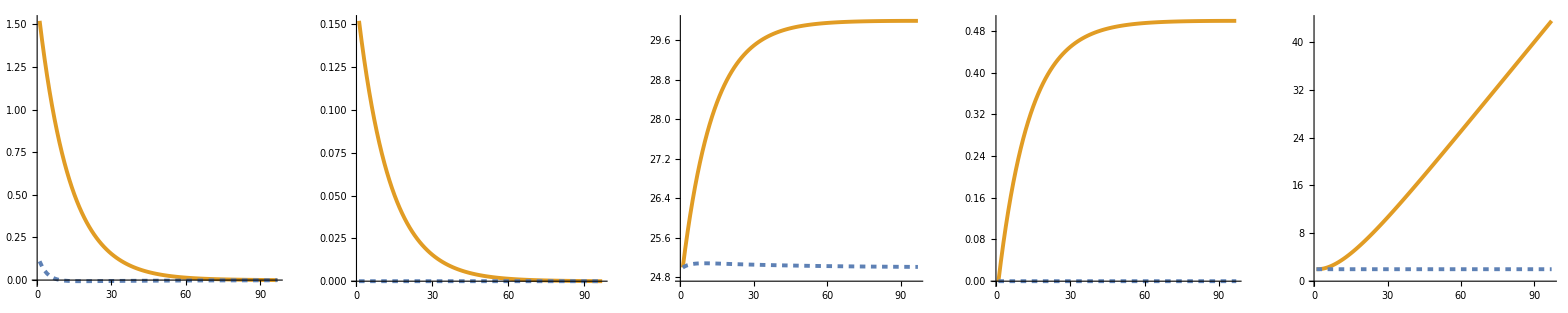

Iteration 2

General::munfl: Exp[-2178.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2117.83] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2128.11] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(96) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(95) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(94) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(93) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(92) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(91) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(90) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(89) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(88) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(87) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(86) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(85) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(84) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(83) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(82) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(81) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(80) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(79) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(78) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(77) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(76) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(75) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(74) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(73) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(72) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(71) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(70) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(69) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(68) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(67) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(66) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(65) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(64) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(63) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(62) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(61) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(60) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(59) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(58) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(57) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(56) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(55) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(54) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(53) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(52) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(51) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(50) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(49) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(48) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(47) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(46) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(45) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(44) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(43) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(42) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(41) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(40) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(39) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(38) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(37) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(36) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(35) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(34) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(33) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(32) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(31) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(30) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(29) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(28) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(27) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96)(ux
1.51987
1.40437
1.29765
1.19904
1.10792
1.02372
0.945925
0.87404
0.807619
0.746245
0.689535
0.637134
0.588716
0.543977
0.502638
0.46444
0.429146
0.396533
0.366399
0.338555
0.312826
0.289053
0.267086
0.246789
0.228034
0.210705
0.194692
0.179896
0.166224
0.153592
0.141919
0.131133
0.121167
0.111958
0.103449
0.0955867
0.0883215
0.0816084
0.0754053
0.0696735
0.0643772
0.0594833
0.0549611
0.0507824
0.0469211
0.043353
0.0400559
0.0370092
0.0341937
0.031592
0.0291878
0.0269659
0.0249126
0.023015
0.0212612
0.0196403
0.0181422
0.0167575
0.0154775
0.0142942
0.0132003
0.0121888
0.0112536
0.0103887
0.00958867
0.00884861
0.00816386
0.00753012
0.00694346
0.00640019
0.00589692
0.0054305
0.00499803
0.00459679
0.00422429
0.00387818
0.00355632
0.00325668
0.0029774
0.00271672
0.00247303
0.00224479
0.00203058
0.00182906
0.00163897
0.00145913
0.0012884
0.00112573
0.000970098
0.000820526
0.000676082
0.000535864
0.000398994
0.000264619
0.000131897
0.
0.)(uy
0.25474
0.230293
0.205873
0.181506
0.157235
0.133129
0.109281
0.0858104
0.0628669
0.040631
0.0193168
-0.00082615
-0.0195108
-0.036412
-0.0511657
-0.0633705
-0.0725907
-0.0783616
-0.0801992
-0.0776139
-0.0701312
-0.0573192
-0.0388264
-0.0144291
0.0159125
0.0519967
0.730474
0.143278
-0.332938
-0.606866
-0.660595
-0.535743
-0.308169
-0.0604456
0.140458
0.256021
0.278689
0.226017
0.130009
0.0255005
-0.0592558
-0.108009
-0.117572
-0.0953508
-0.0548474
-0.010758
0.0249985
0.0455663
0.0496006
0.0402261
0.0231387
0.00453854
-0.0105463
-0.0192233
-0.0209252
-0.0169704
-0.00976166
-0.00191469
0.0044492
0.00810982
0.00882784
0.00715938
0.0041182
0.000807762
-0.00187701
-0.00342133
-0.00372424
-0.00302037
-0.00173737
-0.000340775
0.000791862
0.00144337
0.00157116
0.00127422
0.000732951
0.000143764
-0.000334067
-0.000608924
-0.000662835
-0.00053756
-0.000309214
-0.0000606506
0.000140934
0.00025689
0.000279634
0.000226783
0.00013045
0.000025587
-0.0000594567
-0.000108375
-0.00011797
-0.0000956742
-0.0000550334
-0.0000107945
0.0000250833
0.0000457208
0.)(x
15.
40.0475
65.4714
91.243
117.336
143.726
170.39
197.308
224.46
251.828
279.396
307.149
335.073
363.155
391.382
419.745
448.231
476.833
505.541
534.347
563.244
592.224
621.282
650.412
679.608
708.865
738.178
767.544
796.958
826.416
855.915
885.453
915.026
944.631
974.266
1003.93
1033.62
1063.33
1093.06
1122.82
1152.59
1182.38
1212.19
1242.01
1271.84
1301.69
1331.55
1361.42
1391.3
1421.18
1451.08
1480.99
1510.9
1540.82
1570.74
1600.67
1630.61
1660.55
1690.49
1720.44
1750.4
1780.35
1810.31
1840.28
1870.24
1900.21
1930.18
1960.15
1990.13
2020.11
2050.08
2080.06
2110.05
2140.03
2170.01
2200.
2229.98
2259.97
2289.96
2319.95
2349.94
2379.93
2409.92
2439.91
2469.9
2499.89
2529.89
2559.88
2589.87
2619.87
2649.86
2679.86
2709.85
2739.85
2769.84
2799.83
2829.83)(y
2.
2.00796
2.07884
2.20653
2.38493
2.60795
2.86952
3.16363
3.48433
3.82576
4.18221
4.54815
4.9183
5.28765
5.6516
6.00599
6.3472
6.67228
6.97903
7.26614
7.53327
7.78124
8.01207
8.22915
8.43729
8.64277
8.85335
9.09814
9.50719
9.93719
10.2754
10.4602
10.4837
10.3805
10.2079
10.0265
9.88382
9.80586
9.79592
9.83949
9.91229
9.98882
10.049
10.0819
10.0861
10.0677
10.037
10.0047
9.97932
9.96545
9.96368
9.97143
9.98439
9.99801
10.0087
10.0146
10.0153
10.0121
10.0066
10.0008
9.99632
9.99385
9.99354
9.99492
9.99722
9.99965
10.0016
10.0026
10.0027
10.0021
10.0012
10.0001
9.99935
9.99891
9.99885
9.9991
9.99951
9.99994
10.0003
10.0005
10.0005
10.0004
10.0002
10.
9.99988
9.99981
9.9998
9.99984
9.99991
9.99999
10.
10.0001
10.0001
10.0001
10.
10.
9.99998)(vx
25.
25.38
25.7311
26.0555
26.3552
26.6322
26.8881
27.1246
27.3431
27.545
27.7316
27.904
28.0633
28.2104
28.3464
28.4721
28.5882
28.6955
28.7946
28.8862
28.9709
29.0491
29.1213
29.1881
29.2498
29.3068
29.3595
29.4082
29.4531
29.4947
29.5331
29.5686
29.6014
29.6316
29.6596
29.6855
29.7094
29.7315
29.7519
29.7707
29.7881
29.8042
29.8191
29.8329
29.8455
29.8573
29.8681
29.8781
29.8874
29.8959
29.9038
29.9111
29.9179
29.9241
29.9298
29.9352
29.9401
29.9446
29.9488
29.9527
29.9562
29.9595
29.9626
29.9654
29.968
29.9704
29.9726
29.9747
29.9765
29.9783
29.9799
29.9813
29.9827
29.984
29.9851
29.9862
29.9871
29.988
29.9888
29.9896
29.9903
29.9909
29.9914
29.9919
29.9924
29.9928
29.9932
29.9935
29.9938
29.994
29.9942
29.9944
29.9945
29.9946
29.9947
29.9947
29.9947)(vy
0.
0.063685
0.121258
0.172726
0.218103
0.257412
0.290694
0.318014
0.339467
0.355183
0.365341
0.37017
0.369964
0.365086
0.355983
0.343192
0.327349
0.309201
0.289611
0.269561
0.250158
0.232625
0.218295
0.208589
0.204981
0.208959
0.221959
0.404577
0.440397
0.357162
0.205446
0.040297
-0.0936388
-0.170681
-0.185792
-0.150678
-0.0866724
-0.0170003
0.0395039
0.072006
0.0783811
0.0635672
0.0365649
0.00717201
-0.0166657
-0.0303775
-0.033067
-0.0268174
-0.0154258
-0.00302569
0.00703084
0.0128155
0.0139502
0.0113136
0.00650777
0.00127646
-0.00296613
-0.00540655
-0.00588522
-0.00477292
-0.00274547
-0.000538508
0.00125134
0.00228089
0.00248283
0.00201358
0.00115824
0.000227183
-0.000527908
-0.00096225
-0.00104744
-0.000849478
-0.000488634
-0.0000958428
0.000222711
0.000405949
0.00044189
0.000358373
0.000206143
0.0000404337
-0.0000939563
-0.00017126
-0.000186422
-0.000151189
-0.0000869664
-0.000017058
0.0000396378
0.0000722502
0.000078647
0.0000637828
0.0000366889
7.19633×10^-6
-0.0000167222
-0.0000304806
-0.0000331792
-0.0000269084
-0.0000154781)

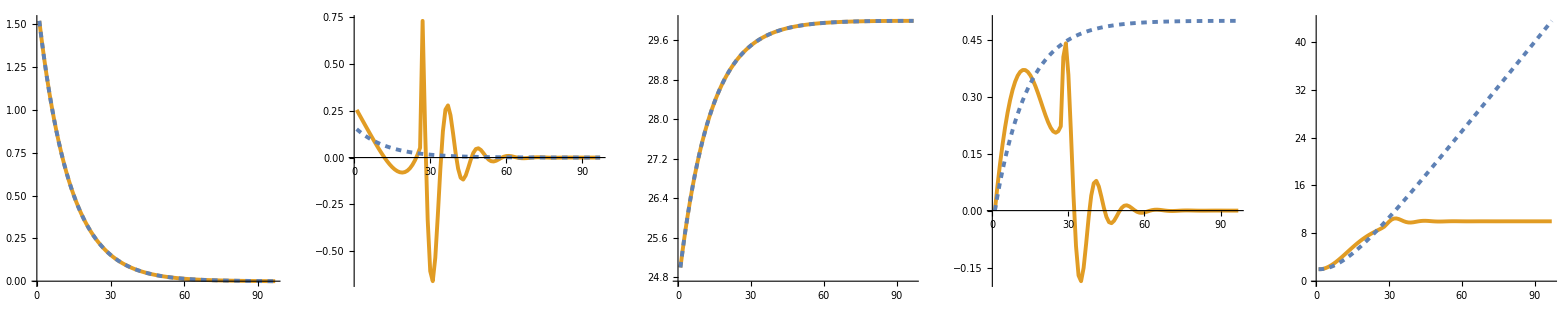

Iteration 3

(94) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(91) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(90) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(87) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(86) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(84) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(83) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(82) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(81) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(80) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(79) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(77) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(76) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(75) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(74) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(70) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(69) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(68) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(67) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(64) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(63) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(62) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(61) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(58) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(56) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(52) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(47) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(45) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(44) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(42) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(40) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(36) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(35) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(33) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(32) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(31) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(29) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96)(ux
1.51987
1.40437
1.29765
1.19904
1.10792
1.02372
0.945925
0.87404
0.807619
0.746245
0.689535
0.637134
0.588716
0.543977
0.502638
0.46444
0.429146
0.396533
0.366399
0.338555
0.312826
0.289053
0.267086
0.246789
0.228034
0.210705
0.194692
0.179896
0.166224
0.153592
0.141919
0.131133
0.121167
0.111958
0.103449
0.0955867
0.0883215
0.0816084
0.0754053
0.0696735
0.0643772
0.0594833
0.0549611
0.0507824
0.0469211
0.043353
0.0400559
0.0370092
0.0341937
0.031592
0.0291878
0.0269659
0.0249126
0.023015
0.0212612
0.0196403
0.0181422
0.0167575
0.0154775
0.0142942
0.0132003
0.0121888
0.0112536
0.0103887
0.00958867
0.00884861
0.00816386
0.00753012
0.00694346
0.00640019
0.00589692
0.0054305
0.00499803
0.00459679
0.00422429
0.00387818
0.00355632
0.00325668
0.0029774
0.00271672
0.00247303
0.00224479
0.00203058
0.00182906
0.00163897
0.00145913
0.0012884
0.00112573
0.000970098
0.000820526
0.000676082
0.000535864
0.000398994
0.000264619
0.000131897
0.
0.)(uy
0.133068
0.121902
0.113004
0.106146
0.101078
0.0975264
0.0951859
0.0937237
0.0927768
0.0919519
0.0908276
0.0889572
0.0858746
0.0811025
0.0741657
0.064609
0.0520223
0.036074
0.0165557
-0.00655879
-0.0330376
-0.062293
-0.0932562
-0.124219
-0.152635
-0.17486
-0.185829
-0.178598
0.313664
-0.227873
-0.12028
-0.237904
-0.266646
-0.00304382
-0.241576
-0.141583
0.00680416
0.00308554
0.0227077
0.173317
0.0335363
0.160251
0.0302324
0.0552094
-0.00488449
-0.0182001
-0.0847042
-0.0261681
-0.0345824
-0.0382316
-0.0354824
-0.0465425
-0.000822408
0.0116712
0.0235809
0.0490014
0.0240776
0.0348115
0.0075661
0.000367298
-0.00876744
-0.0160397
-0.017484
-0.0141962
-0.00422256
-0.00168741
0.00076103
0.00432385
0.005915
0.00562962
0.00220549
0.00147559
0.000611423
-0.000251841
-0.00141309
-0.00193075
-0.00183631
0.000259722
-0.00136543
-0.000676816
8.84973×10^-6
0.000520887
0.000774693
0.000771374
0.0081606
-0.00350675
-0.00379601
0.0137513
0.00914728
-0.018385
-0.0151341
0.0212678
0.0127213
-0.0263476
0.0124355
0.
0.)(x
15.
40.0475
65.4714
91.243
117.336
143.726
170.39
197.308
224.46
251.828
279.396
307.149
335.073
363.155
391.382
419.745
448.231
476.833
505.541
534.347
563.244
592.224
621.282
650.412
679.608
708.865
738.178
767.544
796.958
826.416
855.915
885.453
915.026
944.631
974.266
1003.93
1033.62
1063.33
1093.06
1122.82
1152.59
1182.38
1212.19
1242.01
1271.84
1301.69
1331.55
1361.42
1391.3
1421.18
1451.08
1480.99
1510.9
1540.82
1570.74
1600.67
1630.61
1660.55
1690.49
1720.44
1750.4
1780.35
1810.31
1840.28
1870.24
1900.21
1930.18
1960.15
1990.13
2020.11
2050.08
2080.06
2110.05
2140.03
2170.01
2200.
2229.98
2259.97
2289.96
2319.95
2349.94
2379.93
2409.92
2439.91
2469.9
2499.89
2529.89
2559.88
2589.87
2619.87
2649.86
2679.86
2709.85
2739.85
2769.84
2799.83
2829.83)(y
2.
2.00416
2.04123
2.10851
2.20382
2.32551
2.47235
2.64351
2.83842
3.05672
3.2982
3.56263
3.84971
4.15893
4.48947
4.84007
5.20891
5.59351
5.99062
6.39613
6.80506
7.21153
7.60882
7.98957
8.34604
8.67057
8.95624
9.19786
9.39324
9.55936
9.78697
9.96098
10.1012
10.1811
10.2026
10.2158
10.1718
10.097
10.0238
9.95202
9.89059
9.86812
9.858
9.88387
9.91809
9.96423
10.0087
10.0466
10.0651
10.0769
10.0798
10.0733
10.0576
10.0316
10.0059
9.98344
9.96767
9.96337
9.96543
9.97534
9.98691
9.99829
10.0073
10.0122
10.0128
10.0102
10.0066
10.0027
9.9991
9.99661
9.99559
9.99587
9.99668
9.99784
9.99912
10.0003
10.0011
10.0014
10.0014
10.0013
10.001
10.0004
9.99995
9.99959
9.99942
9.99968
10.0016
10.0027
10.0033
10.0072
10.0126
10.0135
10.0117
10.015
10.0202
10.0201
10.0227)(vx
25.
25.38
25.7311
26.0555
26.3552
26.6322
26.8881
27.1246
27.3431
27.545
27.7316
27.904
28.0633
28.2104
28.3464
28.4721
28.5882
28.6955
28.7946
28.8862
28.9709
29.0491
29.1213
29.1881
29.2498
29.3068
29.3595
29.4082
29.4531
29.4947
29.5331
29.5686
29.6014
29.6316
29.6596
29.6855
29.7094
29.7315
29.7519
29.7707
29.7881
29.8042
29.8191
29.8329
29.8455
29.8573
29.8681
29.8781
29.8874
29.8959
29.9038
29.9111
29.9179
29.9241
29.9298
29.9352
29.9401
29.9446
29.9488
29.9527
29.9562
29.9595
29.9626
29.9654
29.968
29.9704
29.9726
29.9747
29.9765
29.9783
29.9799
29.9813
29.9827
29.984
29.9851
29.9862
29.9871
29.988
29.9888
29.9896
29.9903
29.9909
29.9914
29.9919
29.9924
29.9928
29.9932
29.9935
29.9938
29.994
29.9942
29.9944
29.9945
29.9946
29.9947
29.9947
29.9947)(vy
0.
0.0332669
0.0637425
0.0919935
0.11853
0.143799
0.168181
0.191978
0.215408
0.238603
0.261591
0.284298
0.306537
0.328005
0.348281
0.366822
0.382975
0.39598
0.404999
0.409138
0.407498
0.399239
0.383665
0.360351
0.329297
0.291138
0.247423
0.200966
0.156316
0.234732
0.177764
0.147694
0.088218
0.0215566
0.0207956
-0.0395982
-0.0749941
-0.0732931
-0.0725217
-0.0668447
-0.0235156
-0.0151315
0.0249311
0.0324892
0.0462916
0.0450705
0.0405204
0.0193444
0.0128024
0.00415674
-0.00540117
-0.0142718
-0.0259074
-0.026113
-0.0231952
-0.0173
-0.00504967
0.00096974
0.00967262
0.0115641
0.011656
0.00946411
0.00545419
0.0010832
-0.00246584
-0.00352148
-0.00394334
-0.00375308
-0.00267212
-0.00119336
0.00021404
0.000765413
0.00113431
0.00128717
0.00122421
0.000870934
0.000388247
-0.0000708303
-5.89982×10^-6
-0.000347258
-0.000516462
-0.000514249
-0.000384028
-0.000190355
2.48899×10^-6
0.00204264
0.00116595
0.000216949
0.00365479
0.00594161
0.00134535
-0.00243817
0.00287878
0.00605912
-0.000527782
0.00258109
0.00258109)

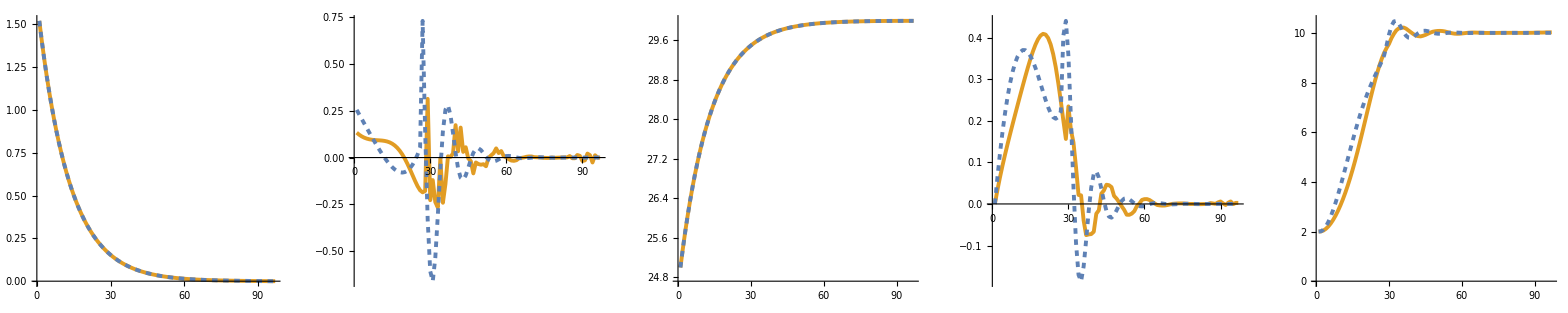

Iteration 4

(96) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(95) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(94) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(93) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(92) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(91) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(90) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(89) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(88) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(87) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(86) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(85) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(84) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(83) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(82) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(81) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(80) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(79) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(78) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(77) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(76) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(75) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(74) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(70) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(69) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(68) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(67) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(66) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(65) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(64) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(62) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(61) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(56) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(53) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(52) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(51) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(50) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(49) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(48) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(47) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(46) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(45) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(44) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(40) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(37) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(36) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(35) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(34) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(33) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(32) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(29) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(k
0
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96)(ux
1.51987
1.40437
1.29765
1.19904
1.10792
1.02372
0.945925
0.87404
0.807619
0.746245
0.689535
0.637134
0.588716
0.543977
0.502638
0.46444
0.429146
0.396533
0.366399
0.338555
0.312826
0.289053
0.267086
0.246789
0.228034
0.210705
0.194692
0.179896
0.166224
0.153592
0.141919
0.131133
0.121167
0.111958
0.103449
0.0955867
0.0883215
0.0816084
0.0754053
0.0696735
0.0643772
0.0594833
0.0549611
0.0507824
0.0469211
0.043353
0.0400559
0.0370092
0.0341937
0.031592
0.0291878
0.0269659
0.0249126
0.023015
0.0212612
0.0196403
0.0181422
0.0167575
0.0154775
0.0142942
0.0132003
0.0121888
0.0112536
0.0103887
0.00958867
0.00884861
0.00816386
0.00753012
0.00694346
0.00640019
0.00589692
0.0054305
0.00499803
0.00459679
0.00422429
0.00387818
0.00355632
0.00325668
0.0029774
0.00271672
0.00247303
0.00224479
0.00203058
0.00182906
0.00163897
0.00145913
0.0012884
0.00112573
0.000970098
0.000820526
0.000676082
0.000535864
0.000398994
0.000264619
0.000131897
0.
0.)(uy
0.146711
0.134331
0.122623
0.11153
0.101019
0.0910843
0.081744
0.0730392
0.0650318
0.0578007
0.0514366
0.046035
0.0416865
0.0384644
0.0364086
0.0355053
0.0356621
0.0366772
0.0382034
0.0397066
0.0404196
0.0392947
0.0349602
0.0256909
0.00941166
-0.0162358
-0.053704
-0.105126
0.11783
-0.412612
-0.414686
-0.502757
-0.413864
-0.243729
-0.0551953
0.100004
0.191402
0.147887
0.127054
0.174755
0.0059685
-0.0184675
-0.0410746
-0.016016
-0.0384901
-0.0457231
-0.0397171
-0.0252833
-0.00813717
0.00675675
0.016238
0.0192894
0.0167557
0.015615
0.00455514
-0.00712312
-0.0118675
-0.0132772
-0.0120072
-0.00643077
0.0091795
0.0103233
0.00329643
0.00780998
0.00393874
0.0000506231
-0.00287812
-0.00435515
-0.00437413
-0.00329484
-0.000864249
-0.000488845
0.000180901
0.00190719
0.00205611
0.00165378
0.000938583
0.00016754
-0.000452627
-0.000804596
-0.000867423
-0.000697688
-0.000395965
-0.0000706809
0.000190952
0.000339439
0.000365944
0.000294337
0.000167048
0.0000298185
-0.0000805579
-0.000143201
-0.000154383
-0.000124173
-0.0000704732
-0.0000125797
0.)(x
15.
40.0475
65.4714
91.243
117.336
143.726
170.39
197.308
224.46
251.828
279.396
307.149
335.073
363.155
391.382
419.745
448.231
476.833
505.541
534.347
563.244
592.224
621.282
650.412
679.608
708.865
738.178
767.544
796.958
826.416
855.915
885.453
915.026
944.631
974.266
1003.93
1033.62
1063.33
1093.06
1122.82
1152.59
1182.38
1212.19
1242.01
1271.84
1301.69
1331.55
1361.42
1391.3
1421.18
1451.08
1480.99
1510.9
1540.82
1570.74
1600.67
1630.61
1660.55
1690.49
1720.44
1750.4
1780.35
1810.31
1840.28
1870.24
1900.21
1930.18
1960.15
1990.13
2020.11
2050.08
2080.06
2110.05
2140.03
2170.01
2200.
2229.98
2259.97
2289.96
2319.95
2349.94
2379.93
2409.92
2439.91
2469.9
2499.89
2529.89
2559.88
2589.87
2619.87
2649.86
2679.86
2709.85
2739.85
2769.84
2799.83
2829.83)(y
2.
2.00458
2.04546
2.11955
2.22395
2.35591
2.51281
2.69219
2.89173
3.10929
3.34287
3.59071
3.85123
4.12313
4.40535
4.69712
4.99797
5.3077
5.62637
5.95426
6.29175
6.63919
6.9967
7.36389
7.73954
8.1211
8.50421
8.8821
9.24495
9.58848
9.9449
10.1981
10.3449
10.3687
10.2944
10.1651
10.0268
9.91643
9.8525
9.82489
9.83054
9.8746
9.91939
9.95886
9.98884
10.0141
10.0295
10.0337
10.0284
10.0174
10.0047
9.99404
9.98754
9.98577
9.98816
9.99411
10.0008
10.0056
10.0074
10.0059
10.0016
9.99612
9.99301
9.99225
9.99246
9.99451
9.99741
10.0002
10.0023
10.0033
10.0032
10.0023
10.0013
10.0002
9.99912
9.99856
9.9985
9.99883
9.99937
9.99993
10.0004
10.0006
10.0006
10.0005
10.0003
10.
9.99984
9.99974
9.99973
9.99979
9.99989
9.99999
10.0001
10.0001
10.0001
10.0001
10.)(vx
25.
25.38
25.7311
26.0555
26.3552
26.6322
26.8881
27.1246
27.3431
27.545
27.7316
27.904
28.0633
28.2104
28.3464
28.4721
28.5882
28.6955
28.7946
28.8862
28.9709
29.0491
29.1213
29.1881
29.2498
29.3068
29.3595
29.4082
29.4531
29.4947
29.5331
29.5686
29.6014
29.6316
29.6596
29.6855
29.7094
29.7315
29.7519
29.7707
29.7881
29.8042
29.8191
29.8329
29.8455
29.8573
29.8681
29.8781
29.8874
29.8959
29.9038
29.9111
29.9179
29.9241
29.9298
29.9352
29.9401
29.9446
29.9488
29.9527
29.9562
29.9595
29.9626
29.9654
29.968
29.9704
29.9726
29.9747
29.9765
29.9783
29.9799
29.9813
29.9827
29.984
29.9851
29.9862
29.9871
29.988
29.9888
29.9896
29.9903
29.9909
29.9914
29.9919
29.9924
29.9928
29.9932
29.9935
29.9938
29.994
29.9942
29.9944
29.9945
29.9946
29.9947
29.9947
29.9947)(vy
0.
0.0366779
0.0702607
0.100916
0.128799
0.154054
0.176825
0.197261
0.215521
0.231778
0.246229
0.259088
0.270597
0.281018
0.290634
0.299736
0.308613
0.317528
0.326698
0.336248
0.346175
0.35628
0.366104
0.374844
0.381266
0.383619
0.37956
0.366134
0.339853
0.36931
0.266157
0.162486
0.0367969
-0.0666692
-0.127601
-0.1414
-0.116399
-0.0685488
-0.0315769
0.000186649
0.0438755
0.0453676
0.0407507
0.0304821
0.0264781
0.0168556
0.00542478
-0.0045045
-0.0108253
-0.0128596
-0.0111704
-0.00711094
-0.00228858
0.00190034
0.0058041
0.00694288
0.0051621
0.00219522
-0.00112408
-0.00412587
-0.00573356
-0.00343868
-0.000857856
-0.0000337488
0.00191875
0.00290343
0.00291609
0.00219656
0.00110777
0.0000142378
-0.000809471
-0.00102553
-0.00114774
-0.00110252
-0.000625722
-0.000111693
0.000301752
0.000536397
0.000578282
0.000465125
0.000263976
0.0000471206
-0.000127301
-0.000226293
-0.000243963
-0.000196225
-0.000111365
-0.000019879
0.0000537053
0.0000954672
0.000102922
0.0000827823
0.0000469821
8.38645×10^-6
-0.0000226569
-0.0000402752
-0.0000434201)

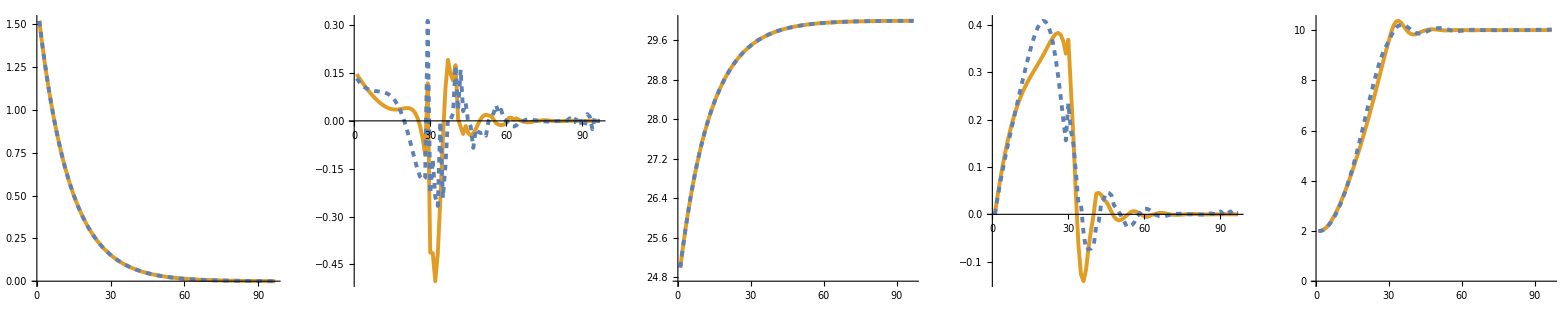

Iteration 5

(96) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(95) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(94) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(93) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(92) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(88) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(87) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(83) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(82) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(81) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(80) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(79) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(78) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(77) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(74) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(71) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(70) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(69) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(67) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(66) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(65) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(64) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(62) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(61) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(56) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(55) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(54) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(50) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(48) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

(47) Constraint Activation (rbUp)

{{0,1.,0,1.875}}

$Aborted

```mathematica
Differential Dynamic Programming;
it=0;
costFullPrev=1000000;
While[True,
StringForm["Iteration ``",it+1]//Print;
alphaStore=Table[{},{i,1,K}];betaStore=Table[{},{i,1,K}];
PPStore=Table[{},{i,1,K}];QQStore=Table[{},{i,1,K}];constStore=Table[0.0,{i,1,K}];

dx1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dx+dvx*T+0.5*dax*T^2;
dy1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dy+dvy*T+0.5*day*T^2;
dvx1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dvx+dax*T;
dvy1[dx_,dy_,dvx_,dvy_,dax_,day_]:=dvy+day*T;


(*k=K*)
xPoint=xInit[[K]];vxPoint=vxInit[[K]];axPoint=axInit[[K]];
yPoint=yInit[[K]];vyPoint=vyInit[[K]];ayPoint=ayInit[[K]];

AA=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});EE=({{0}, {0}, {0}, {0}});

PP=AA;QQ=EE;
V[dx_,dy_,dvx_,dvy_,PP_,QQ_]:=0.5*({{dx, dy, dvx, dvy}}).PP.({{dx}, {dy}, {dvx}, {dvy}})+({{dx, dy, dvx, dvy}}).QQ;
alpha=({{0}, {0}});beta=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
alphaStore[[K]]=alpha;betaStore[[K]]=beta;
PPStore[[K]]=PP;QQStore[[K]]=QQ;


(* k<=K-1 *)
For[k=K-1,k≥1,k--,
xPoint=xInit[[k]];vxPoint=vxInit[[k]];axPoint=axInit[[k]];
yPoint=yInit[[k]];vyPoint=vyInit[[k]];ayPoint=ayInit[[k]];

ayUp[ayPoint_]:=-(ayMax-ayPoint);ayLow[ayPoint_]:=ayMin-ayPoint;
axUp[axPoint_]:=-(axMax-axPoint);axLow[axPoint_]:=axMin-axPoint;
rbu[dy_,dvy_]:=-(-ayPoint-dy*Klat+dvy*(-2.0*Sqrt[Klat]+(Klat*T)/2.0)+(-2.0*Sqrt[Klat]+(Klat*T)/2.0)*vyPoint+Klat*(yMax-yPoint));
rbl[dy_,dvy_]:=(-ayPoint-dy*Klat+dvy*(-2.0*Sqrt[Klat]+(Klat*T)/2.0)+(-2.0*Sqrt[Klat]+(Klat*T)/2.0)*vyPoint+Klat*(yMin-yPoint));


axTaylor[dax_]:=0.5*dax^2+axPoint* dax+0.5*axPoint^2;
ayTaylor[day_]:=0.5*day^2+ayPoint* day+0.5*ayPoint^2;
vxTaylor[dvx_]:=0.5*dvx^2+(vxPoint-vdx)* dvx+0.5*(vxPoint-vdx)^2;
vyTaylor[dvy_]:=0.5*dvy^2+(vyPoint-vdy)* dvy+0.5*(vyPoint-vdy)^2;
ellipseTaylor[dx_,dy_,dvx_,dvy_,obsx_,obsy_]:=E^(-Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])+(dx*obsx+dy*obsy*p-dx*xPoint-dy*p*yPoint)/(E^Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])+(dx^2*obsx^4+2*dx*dy*obsx^3*obsy*p+dx^2*obsx^2*obsy^2*p+dy^2*obsx^2*obsy^2*p^2+2*dx*dy*obsx*obsy^3*p^2+dy^2*obsy^4*p^3-4*dx^2*obsx^3*xPoint-6*dx*dy*obsx^2*obsy*p*xPoint-2*dx^2*obsx*obsy^2*p*xPoint-2*dy^2*obsx*obsy^2*p^2*xPoint-2*dx*dy*obsy^3*p^2*xPoint+6*dx^2*obsx^2*xPoint^2+6*dx*dy*obsx*obsy*p*xPoint^2+dx^2*obsy^2*p*xPoint^2+dy^2*obsy^2*p^2*xPoint^2-4*dx^2*obsx*xPoint^3-2*dx*dy*obsy*p*xPoint^3+dx^2*xPoint^4-2*dx*dy*obsx^3*p*yPoint-2*dx^2*obsx^2*obsy*p*yPoint-2*dy^2*obsx^2*obsy*p^2*yPoint-6*dx*dy*obsx*obsy^2*p^2*yPoint-4*dy^2*obsy^3*p^3*yPoint+6*dx*dy*obsx^2*p*xPoint*yPoint+4*dx^2*obsx*obsy*p*xPoint*yPoint+4*dy^2*obsx*obsy*p^2*xPoint*yPoint+6*dx*dy*obsy^2*p^2*xPoint*yPoint-6*dx*dy*obsx*p*xPoint^2*yPoint-2*dx^2*obsy*p*xPoint^2*yPoint-2*dy^2*obsy*p^2*xPoint^2*yPoint+2*dx*dy*p*xPoint^3*yPoint+dx^2*obsx^2*p*yPoint^2+dy^2*obsx^2*p^2*yPoint^2+6*dx*dy*obsx*obsy*p^2*yPoint^2+6*dy^2*obsy^2*p^3*yPoint^2-2*dx^2*obsx*p*xPoint*yPoint^2-2*dy^2*obsx*p^2*xPoint*yPoint^2-6*dx*dy*obsy*p^2*xPoint*yPoint^2+dx^2*p*xPoint^2*yPoint^2+dy^2*p^2*xPoint^2*yPoint^2-2*dx*dy*obsx*p^2*yPoint^3-4*dy^2*obsy*p^3*yPoint^3+2*dx*dy*p^2*xPoint*yPoint^3+dy^2*p^3*yPoint^4-dy^2*obsx^2*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx*dy*obsx*obsy*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dx^2*obsy^2*p*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dy^2*obsx*p*xPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-2*dx*dy*obsy*p*xPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dy^2*p*xPoint^2*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-2*dx*dy*obsx*p*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx^2*obsy*p*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]+2*dx*dy*p*xPoint*yPoint*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]-dx^2*p*yPoint^2*Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2])/(2*E^Sqrt[obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2]*(obsx^2+obsy^2*p-2*obsx*xPoint+xPoint^2-2*obsy*p*yPoint+p*yPoint^2)^2);

L[dx_,dy_,dvx_,dvy_,dax_,day_,PP_,QQ_]:=w1*axTaylor[dax]+w2*ayTaylor[day]+w3*vxTaylor[dvx]+w4*vyTaylor[dvy]+w5*Sum[ellipseTaylor[dx,dy,dvx,dvy,xObs[[i,k]],yObs[[i,k]]],{i,1,numObs}]
+V[dx1[dx,dy,dvx,dvy,dax,day],dy1[dx,dy,dvx,dvy,dax,day],dvx1[dx,dy,dvx,dvy,dax,day],dvy1[dx,dy,dvx,dvy,dax,day],PP,QQ][[1,1]];

(*x^T.B.x*)
dxdx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dx,2}];dxdy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dy];
dxdvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dvx];dxdvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx,dvy];
dydx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dx];dydy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dy,2}];
dydvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dvx];dydvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy,dvy];
dvxdx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dx];dvxdy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dy];
dvxdvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dvx,2}];dvxdvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx,dvy];
dvydx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dx];dvydy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dy];
dvydvx=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy,dvx];dvydvy=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dvy,2}];
AA=({{dxdx, dxdy, dxdvx, dxdvy}, {dydx, dydy, dydvx, dydvy}, {dvxdx, dvxdy, dvxdvx, dvxdvy}, {dvydx, dvydy, dvydvx, dvydvy}});

(*a^T.B.x*)
xaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx dax];yaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy dax];
vxaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx dax];vyaxCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy dax];
xayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx day];yayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy day];
vxayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx day];vyayCoeff=Coefficient[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy day];
BB=({{xaxCoeff, xayCoeff}, {yaxCoeff, yayCoeff}, {vxaxCoeff, vxayCoeff}, {vyaxCoeff, vyayCoeff}});

(*a^T.B.a*)
daxdax=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{dax,2}];dayday=D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],{day,2}];
CC=({{daxdax, 0}, {0, dayday}});
(*a^T.D*)
axcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dax],{dax,day,dx,dy,dvx,dvy}];
aycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],day],{dax,day,dx,dy,dvx,dvy}];
If[axcl=={},axCoeff=0.0,axCoeff=axcl[[1,1,1,1,1,1]]];If[aycl=={},ayCoeff=0.0,ayCoeff=aycl[[1,1,1,1,1,1]]];

DD=({{axCoeff}, {ayCoeff}});
(*x^T.E*)
xcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dx],{dax,day,dx,dy,dvx,dvy}];
ycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dy],{dax,day,dx,dy,dvx,dvy}];
vxcl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvx],{dax,day,dx,dy,dvx,dvy}];
vycl=CoefficientList[D[L[dx,dy,dvx,dvy,dax,day,PP,QQ],dvy],{dax,day,dx,dy,dvx,dvy}];
If[xcl=={},xCoeff=0.0,xCoeff=xcl[[1,1,1,1,1,1]]];If[ycl=={},yCoeff=0.0,yCoeff=ycl[[1,1,1,1,1,1]]];
If[vxcl=={},vxCoeff=0.0,vxCoeff=vxcl[[1,1,1,1,1,1]]];If[vycl=={},vyCoeff=0.0,vyCoeff=vycl[[1,1,1,1,1,1]]];

EE=({{xCoeff}, {yCoeff}, {vxCoeff}, {vyCoeff}});

(*Constrained DDP*)
qq=-DD-Transpose[BB].({{xPoint}, {yPoint}, {vxPoint}, {vyPoint}});
Ct={};d={};R={};
While[True,
(* Active Constraints *)
(*ax bounds*)
(*If[axUp[axPoint]>=0.0,
AppendTo[Ct,{-1,0}];AppendTo[d,{axUp[axPoint]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (axMax)",k]];
If[axMin>=axPoint,
AppendTo[Ct,{1,0}];AppendTo[d,{axLow[axPoint]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (axMin)",k]];*)
(*ay bounds*)
(*If[ayUp>=0.0,
AppendTo[Ct,{0,-1}];AppendTo[d,{ayUp}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (ayMax)",k]//Print];*)
(*If[ayMin>=ayPoint,
AppendTo[Ct,{0,1}];AppendTo[d,{ayLow[ayPoint]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) Constraint Activation (ayMin)",k]//Print];*)
(*road bounds*)
If[rbu[0.0,0.0]>=0.0,
AppendTo[Ct,{0,-1}];AppendTo[d,{rbu[0.0,0.0]}];AppendTo[R,{D[rbu[dy,dvy],dx],D[rbu[dy,dvy],dy],D[rbu[dy,dvy],dvx],D[rbu[dy,dvy],dvy]}];
StringForm["(``) Constraint Activation (rbUp)",k]//Print;];

If[d=={},Ct={{0,0}};d={{0}};R={{0,0,0,0}}];

(* Quadratic Problem for Active Constraints *)
tempCstar=Ct.Inverse[CC].Transpose[Ct];(*(4x2).(2x2).(2x4)->(4x4)*)
If[Det[tempCstar]!=0,tempCstar=Inverse[tempCstar]];
Cstar=tempCstar.Ct.Inverse[CC];(*(4x4).(4x2).(2x2)->(4x2)*)

Hstar=Inverse[CC].(({{1.0, 0.0}, {0.0, 1.0}})-Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)
(*Hstar=Inverse[CC]-(Inverse[CC].Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)*)

pStar=-Hstar.qq+Transpose[Cstar].d;(*(2x2).(2x1)+(2x4).(4x1)->(2x1)*)
lambdaStar=Cstar.qq-tempCstar.d;(*(4x2).(2x1)-(4x4).(4x1)->(4x1)*)

(*If[axLow[axPoint]>pStar[[1,1]],
Ct={};d={};R={};
error=pStar[[1,1]]-axPoint;
AppendTo[Ct,{1,0}];AppendTo[d,{axLow[pStar[[1,1]]]}];AppendTo[R,{0,0,0,0}];
StringForm["(``) pStar: `` | axPoint: `` | c[axPoint]: `` | c[pStar]: ``",k,pStar[[1,1]],axPoint,axLow[axPoint],axLow[pStar[[1,1]]]]//Print;

tempCstar=Ct.Inverse[CC].Transpose[Ct];(*(4x2).(2x2).(2x4)->(4x4)*)
If[Det[tempCstar]!=0,tempCstar=Inverse[tempCstar]];
Cstar=tempCstar.Ct.Inverse[CC];(*(4x4).(4x2).(2x2)->(4x2)*)
Hstar=Inverse[CC]-(Inverse[CC].Transpose[Ct].Cstar);(*(2x2).[(2x2)-(2x4).(4x2)]->(2x2)*)
];*)

P=d;

Break[];
];

(*(2x2).(2x1)+(2x4).(4x1)->(2x1)*)
alpha=-Hstar.DD+Transpose[Cstar].P;
(*(2x2).(2x4)+(2x4).(4x4)->(2x4)*)
beta=-Hstar.Transpose[BB]+Transpose[Cstar].R;
(*MatrixForm[alpha]//Print;*)
PP=AA+Transpose[beta].CC.beta+BB.beta+Transpose[beta].Transpose[BB];
QQ=EE+Transpose[beta].CC.alpha+BB.alpha+Transpose[beta].DD;

alphaStore[[k]]=alpha;betaStore[[k]]=beta;
PPStore[[k]]=PP;QQStore[[k]]=QQ;
];

(* Forward Pass *)
While[True,
axInitNext={};vxInitNext={};xInitNext={};
ayInitNext={};vyInitNext={};yInitNext={};

xDDP=xInit[[1]];vxDDP=vxInit[[1]];
yDDP=yInit[[1]];vyDDP=vyInit[[1]];

vxInitNext=AppendTo[vxInitNext,vxDDP];
vyInitNext=AppendTo[vyInitNext,vyDDP];
xInitNext=AppendTo[xInitNext,xDDP];
yInitNext=AppendTo[yInitNext,yDDP];
costFull=0.0;

For[k=1,k<K,k++,
dxDDP=(xDDP-xInit[[k]]);dvxDDP=(vxDDP-vxInit[[k]]);
dyDDP=(yDDP-yInit[[k]]);dvyDDP=(vyDDP-vyInit[[k]]);

uDDP=({{axInit[[k]]}, {ayInit[[k]]}})+eps*(alphaStore[[k]])+betaStore[[k]].({{dxDDP}, {dyDDP}, {dvxDDP}, {dvyDDP}});
uxDDP=uDDP[[1,1]];uyDDP=uDDP[[2,1]];

xDDP=xDDP+vxDDP+0.5*uxDDP*T^2;
yDDP=yDDP+vyDDP+0.5*uyDDP*T^2;
vxDDP=vxDDP+uxDDP*T;
vyDDP=vyDDP+uyDDP*T;

axInitNext=AppendTo[axInitNext,uxDDP];ayInitNext=AppendTo[ayInitNext,uyDDP];
vxInitNext=AppendTo[vxInitNext,vxDDP];vyInitNext=AppendTo[vyInitNext,vyDDP];
xInitNext=AppendTo[xInitNext,xDDP];yInitNext=AppendTo[yInitNext,yDDP];
];

Break[];
];
AppendTo[axInitNext,0.0];AppendTo[ayInitNext,0.0];
timeSteps=Table[i,{i,0,K-1}];
axPrt=axInitNext;ayPrt=ayInitNext;xPrt=xInitNext;yPrt=yInitNext;vxPrt=vxInitNext;vyPrt=vyInitNext;
Print[MatrixForm[PrependTo[timeSteps,"k"]],MatrixForm[PrependTo[axPrt,"ux"]],MatrixForm[PrependTo[ayPrt,"uy"]],MatrixForm[PrependTo[xPrt,"x"]],MatrixForm[PrependTo[yPrt,"y"]],MatrixForm[PrependTo[vxPrt,"vx"]],MatrixForm[PrependTo[vyPrt,"vy"]]];

(*Plots*)
myPlot[K,15];

If[((Norm[axInitNext-axInit]< epsilon && Norm[ayInitNext-ayInit]< epsilon) || it>=maxIter),
Print["Terminal criterion met |ax - axPrev|: ", Norm[axInitNext-axInit]];
Print["Terminal criterion met |ay - ayPrev|: ", Norm[ayInitNext-ayInit]];
simOutput[K,T];
Break[];
];

axInit=axInitNext;vxInit=vxInitNext;xInit=xInitNext;
ayInit=ayInitNext;vyInit=vyInitNext;yInit=yInitNext;
it=it+1;
]
```